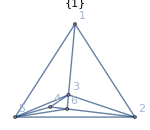
{-Graphics-, | 1 | 2 | 3 | 4 | 5 | 6
1 | 1
0 | 0
1 | 0
1 | 0
1 | 0
1 | 1
0
2 |  | 1
0 | 0
1 | 1
0 | 0
1 | 0
1
3 |  |  | 1
0 | 0
1 | 0
1 | 0
1
4 |  |  |  | 1
0 | 0
1 | 0
1
5 |  |  |  |  | 1
0 | 0
1
6 |  |  |  |  |  | 1
0}

```mathematica
ColorMainMatrix[ReadGrof[3],Graph[#,VertexLabels->"Name",GraphLayout->If[PlanarGraphQ[#],"TutteEmbedding","SpringElectricalEmbedding"],PlotLabel->{ChromaticPolynomial[#,4]/24},ImageSize->150]&]
```

```mathematica
ChromaticPolynomial[ReadGrof[3],x]//Factor
```

(-3+x)^3 (-2+x) (-1+x) x

```mathematica
ChromaticPolynomial[EdgeAdd[ReadGrof[3],1<->4],x]//Factor
```

(-3+x) (-2+x) (-1+x) x (13-7 x+x^2)

```mathematica
ChromaticPolynomial[ReadGrof[3],4]//FactorInteger
```

{{2,3},{3,1}}

```mathematica
ChromaticPolynomial[EdgeAdd[ReadGrof[3],1<->4],4]//FactorInteger
```

{{2,3},{3,1}}

```mathematica
ChromaticPolynomial[VertexContract[ReadGrof[3],{1,4}],4]
```

0

```mathematica
PaintGraph2[ReadGrof[2],"x1==1&&x2==2"]
```

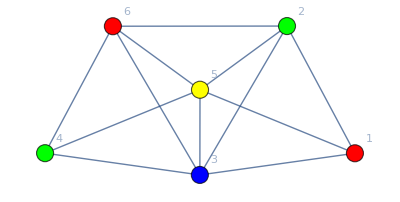
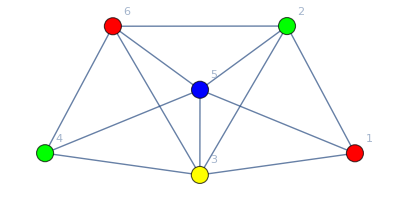

```mathematica
PaintGraph2[ReadGrof[3],"x1==1&&x2==2",GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
```

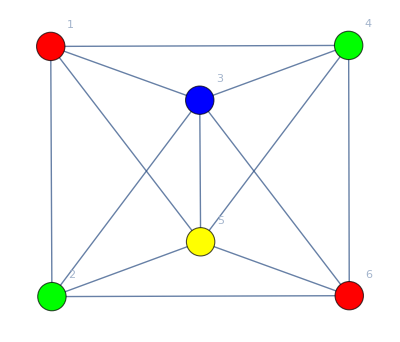
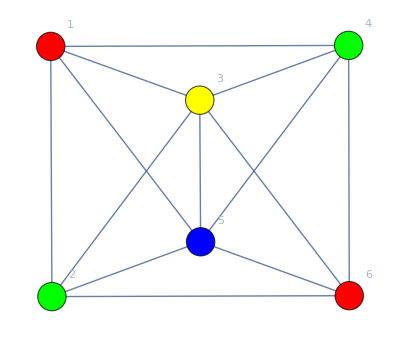

```mathematica
PaintGraph2[EdgeAdd[ReadGrof[3],1<->4],"x1==1&&x2==2",GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
```

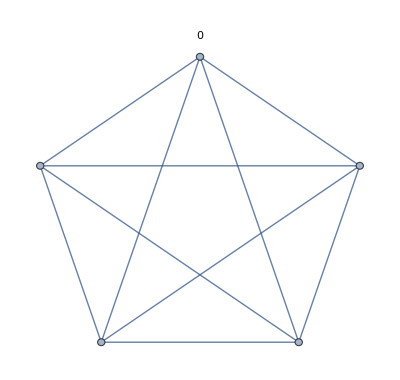
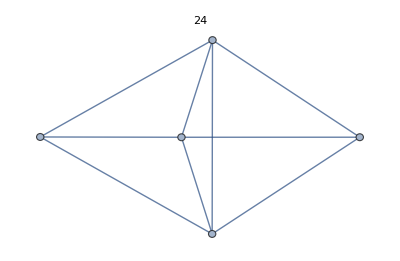
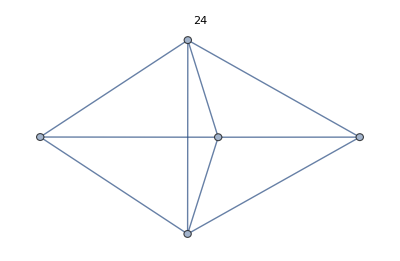
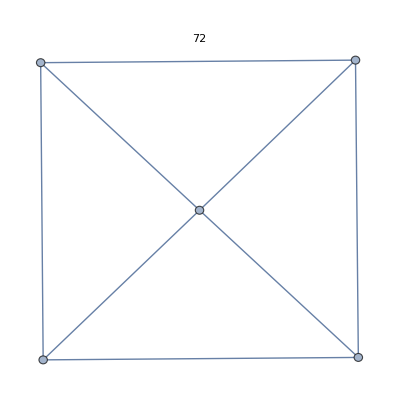
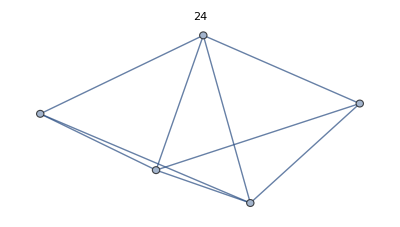
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[With[{g=EdgeContract[EdgeAdd[ReadGrof[3],1<->4],e]},Graph[g,PlotLabel->ChromaticPolynomial[g,4]]],{e,EdgeList[EdgeAdd[ReadGrof[3],1<->4]]}]
```